# Simulating the Emergence of Reproductive and Parenting Strategies using Agent-Based Modeling with Evolutionary Game Theory

## Yash Juneja, Om Kalyani, and Shreraj Sainani - WELP 2025-26

## Abstract

We’ll work on this during the last couple of sprints.

## Introduction

The processes by which life interacts with its environment, sustains itself, and continues on through its posterity (reproduces) are complex and intricately shaped by environmental factors and evolution. One interesting aspect of organism’s behavior is the reasons why organisms reproduce the way they do, and how they take care of their young: their reproductive and parenting behaviors. Agent-Based Modeling (ABM) simulations, while greatly simplified, can provide interesting theory that can provide a basis and a framework for actual studies of ecological behaviors and traits in organisms. Agent-Based Modeling simulations consist of agents that interact with each other and their environment through simple rules. As the simulation evolves through time, the rules produce interesting behavior among the agents that can be studied. These rules ideally mimic real life to create a realistic, albeit simplified, simulation.
	In this work, we apply Agent-Based Modeling and Evolutionary Game Theory in Wolfram Language to create a testing ground for investigating the emergence of reproductive and parenthood strategies in organisms. Specifically, through simulated genes dictating behavior through Evolutionary Game Theory, we explore two areas: 1) fecundity, and 2) parental feeding strategies. [describe fecundity and the feeding strategies in more detail]. With our model, we tweak environment setups, agent behavior, and other parameters of our model to analyze statistical data produced by the simulation and gain insights on reproductive and parenting strategies of organisms. In doing this, we perform experiments with [describe experiments]. Through these experiments, we explore two distinct, but interrelated questions: [questions]
	
[would like to put a bit about r/k selection in here as well, can be found in project plan.]

## High-Level Model Development

### [this is where we will include lit review and research to back up our model choices. I’m thinking that this will be similar to the implementation section of our project proposal and maybe include a little bit of our project plan as well.]

### Current Scope [<-- Replace this with a few sections giving a high-level description of how our model works, so that the following sections have a framing and don’t seem arbitrary.]

Currently, our model simulates the basic behaviors within a population, consisting of agents that move, search for and consume nearby food, and gain or lose energy. We’ve also created a visualization for our ABM so far.

## Legend

CodeText - used to briefly explain smaller specific bits of code.

functionName[] - Text formatted like this references a specific function

parameter - Text formatted like this references a model parameter (see Model Parameters)

## Model Parameters

These are model parameters stored as an association that set the rules for a simulation, and a user may freely tweak them to model certain environmental scenarios or use these as independent variables to run empirical experiments. Most functions of the model take in this parameters association to understand how they should work and to what extent their functions should affect model/agent state. Comments following each parameter outlines its purpose. Parameters, and thus the model, is defined in arbitrary units: arbitrary distance units, arbitrary time units, and arbitrary energy units.

```mathematica
parameters = <| 
  "proximityRadius" -> 0.5, (*How close two things (agent/food, agent/agent, child/parent, etc.) need to be to interact (eat, reproduce, feed, etc.)*)
  "sensingDistance" -> 2, (*How far away agents can sense in arbitrar distance units, and by consequence intentionally travel to, pieces of food or other agents like children and mating partners*)
  "dt" -> 0.1, (*The timestep in arbitrary time units used in the discretization of the simulation*)
  "metabolism" -> 0.2, (*How much energy is expended each timestep by an agent*)
  "foodEnergy" -> 5.0, (*How much energy is gained from one piece of food for an agent*)
  "foodSpawnCooldown" -> 1, (*The cooldown in arbitrary time units of food spawning*)
  "nFoodSpawn" -> 3, (*The number of pieces of food spawned at random locations every time foodSpawnCooldown passes*)
  "nStartingAgents" -> 5, (*The number of agents the simulation starts with*)
  "nStartingFood" -> 7, (*The number of pieces of food that the simulation starts with*)
  "squareBounds" -> {0, 10}, (*The bounds of the model, with both dimensions of the model taking this range of numbers. The lower bound must be zero, and by consequence of this design, the model is square.*)
  "startingEnergy" -> 10, (*The amount of energy an agent starts with*)
  "stepLength" -> 1, (*How far an agent can travel in one timestep, if they choose to travel*)
  "dirChangeProb" -> 0.2, (*If an agent is not intentionally moving and exploring instead, this is the probability at any timestep that they will change their exploration direction.*)
  "lifespan" -> 20, (*How long in arbitrary time units an agent is allowed to live*)
  "maxEnergy" -> 10, (*The most energy an agent can store*)
  "imageSize" -> 500, (*How large, in pixels, the size of the simulation is*)
  "agentSize" -> 0.025, (*The radius of an agent blob in the visualization in aribtrary distance units*)
  "foodSize" -> 0.01, (*The radius of a piece of food in the visualization in aribtrary distance units*)
  "reproductionRadius" -> 1.5, (*FIX - this should be superceded by proximityRadius*)
  "minReproductionEnergy" -> 6.0, (*FIX - The minimmum energy an agent must have to devote its efforts to reproduction opposed to mere survival (confirm this with paper)*)
  "minReproductionAge" -> 2.0, (*FIX - Reproductive maturity age for an agent (is this also the definition of adulthood)*)
  "reproductionEnergyCost" -> 3.0, (*FIX - How much having one child costs. Replace with reproductive energy function*)
  "nextAgentID" -> 1 (*FIX - if this is a holder for the next agent id, and it evolves as the model does, it should go in the model data struct. If it's a parameter for number ID to start at, then it should stay here.*)
|>;
```

To reference a parameter, use the string name of the parameter as the key for the global parameters association. This is how parameters are accessed within our code.

```mathematica
parameters["dt"]
```

0.1

## Core Model

### Data Structures

Before reproductive and parenting functions/strategies were implemented into agents, the core aspects of the model like agents that moved and consumed food were built first. [move up to data structures ^^] The food in a simulation is represented by a list of positions of pieces of food.

createAgent[]is used to initialize agent associations. The data structure for agents was chosen to be an association so that specific attributes of agents that describe their state can be accessed through keys. Each agent attribute is commented with a description of its nature

```mathematica
createAgent[pos_, energy_, age_, id_, currentDirection_, parents_:{-1, -1}] := <|
    "pos" -> pos, (*The current position of an agent, length 2 array*)
    "energy" -> energy, (*The current energy of an agent*)
    "age" -> age, (*The current age of an agent*)
	"id" -> id, (*A unique identifer given to each agent created throughout the history of the simulation instance*)
	"currentDirection" -> currentDirection, (*The current direction the agent is exploring in; value from [0, 2pi)*)
	"parents" -> parents, (*The ids of the agent's parents in a length 2 array. If the agent is one of the primordial starting agents, {-1, -1} is given to this value.*)
    "ancestors" -> ancestors (*FIX - describe functioning of this*)
|>
```

### Core Functions

These functions are the basic operations needed for core model functionality.

For any interactions to occur, an object must be within another’s proximityRadius.  This goes for an agent and a piece of food, an agent and another agent for reproduction, or for a parent and a child.

```mathematica
checkWithinRadius[p1_, p2_, r_] := EuclideanDistance[p1, p2] <= r;
```

EuclidianDistance[] is used in the checkWithinRadius[] function to verify the interaction condition of proximityRadius.

A function called findNearestSensableFoodPosAndI[] is used to find the nearest sensable (within sensingDistance) food to an agent and return its position and index given a list of food to be considered. [fix this-> it doesn’t return the pos and the I, it returns the distance and I]

```mathematica
findNearestSensableFoodPosAndI[agent_, foodPositions_List, params_] := Module[
    {agentPos, foodPosAndI, foodsWithinRadiusPosAndI, dists},
    agentPos = agent["pos"];
    foodPosAndI = Table[{foodPositions[[i]], i}, {i, Length[foodPositions]}];
    foodsWithinRadiusPosAndI = Select[foodPosAndI, checkWithinRadius[agentPos, #[[1]], params["sensingDistance"]]&];
    If[
        Length[foodsWithinRadiusPosAndI] == 0,
        {-1, -1}, (*no food*)
        dists = {EuclideanDistance[agentPos, #[[1]]], #[[2]]}& /@ foodsWithinRadiusPosAndI;
        First@MinimalBy[dists, First]
    ]
]
```

The function first compiles the food positions and indexes, and then isolates the ones that are within sensing distance of the agent. If no pieces of food make it into that isolation, then there are none within sensing distance and {-1, -1} is returned. Else, {closest food’s position, closest food’s index in the food list} is returned.

spawnFoods[]takes in a food list and adds new foods with the amount corresponding to the nFoodSpawn parameter.

```mathematica
spawnFoods[foods_, params_] := Join[foods, RandomReal[params["squareBounds"], {params["nFoodSpawn"], 2}]]
```

To spawn food at the appropriate time, spawnFoodCheck[] updates the model’s food list with a spawnFoods[]operation when appropriate according to the foodSpawnCooldown parameter.

```mathematica
spawnFoodCheck[model_, params_] := Module[
    {model2 = model},
	model2["foods"] = If[
        Mod[model["time"], params["foodSpawnCooldown"]] < 10^(-1),
        spawnFoods[model["foods"], params],
        model["foods"]
    ];
	model2
]
```

< 10^(-1) is used instead of == 0 to not have to worry about integer vs. float mismatch issues.

randomizeAndKill[] is a simulation management function that kills agents if they’ve reached any death conditions and randomizes their order by virtue of shuffling the agent list so that no agents are consistently prioritized over others during iteration in case two or more agents are near the same piece of food or both trying to reproduce with the same agent--the operation will be done on whichever comes first, but it is truly random so long as the order gets randomized during every timestep.

```mathematica
randomizeAndKill[model_, params_] := Module[
    {agents = model["agents"], model2=model},	
	agents = RandomSample[agents];
	model2["agents"] = Select[agents, (#["age"] < params["lifespan"] && #["energy"] > 0)&];
	model2
]
```

metabolizeAgents[]applies the metabolism operation to all agents for a timestep.

```mathematica
metabolizeAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# - params["metabolism"])&, agents, {All, "energy"}];
	model2["agents"] = agents;
	model2
]
```

ageAgents[]ages agents by one timestep dt during a timestep.

```mathematica
ageAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# + params["dt"])&, agents, {All, "age"}];
	model2["agents"] = agents;
	model2
]
```

[explorationWalk[] instead of randomActionWalk[]]

agentEat[]is used to update agents’ energy when they eat a piece of food according to the foodEnergy parameter. The specific food that is being eaten has to be removed concurrently from the model’s food list.

```mathematica
agentEat[agent_, params_] := Module[
    {agent2 = agent, newE},
	newE = agent2["energy"] + params["foodEnergy"];
	agent2["energy"] = If[newE > params["maxEnergy"], params["maxEnergy"], newE];
	agent2
]
```

Through an If[]statement, agentEat[] ensures that the energy does not exceed the maxEnergy

Excluding reproduction [at the moment, (we need to use the paper to see if we should have reproduction in here or outside)], the main agent decision logic for a timestep occurs in the function agentActions. Agents will consume food if they are within the required proximityRadius to eat it, and otherwise they will move following their movement rules:  [if there is a sensable food or instead another agent I can reproduce with (if I have enough energy), move towards it, prioritizing reproduction if possible. Else, explore in a random direction according to direction agent attribute currentDirection I’m currently exploring in. If I’m exploring in a random direction, I have a 0.2 chance this timestep that I’m going to switch directions]

```mathematica
agentActions[model_, params_] :=  Module[
    {model2 = model, agents = model["agents"], foods = model["foods"], agent, nearFoodI, nearFoodDist},
	agents = Table[
		agent = agents[[i]];
		{nearFoodDist, nearFoodI} = findNearestSensableFoodPosAndI[agent, foods, params];
		If[
            nearFoodI>=1 && nearFoodDist < params["proximityRadius"], 
			foods = Delete[foods, nearFoodI]; agentEat[agent, params], 
			randomActionWalk[agent, params]
        ],
	    {i, Length@agents}
    ];
	model2["foods"] = foods;
	model2["agents"] = agents;
	model2
]
```

## Reproduction

Introducing reproduction is crucial to simulate real animal behaviors. When two agents meet, they produce an offspring that inherits a  position between them and a fresh slice of energy. Our functionality has four main parts working together: a way to give every agent an identity, rules for deciding who is allowed to mate with whom, and the reproduction step itself.

Every agent has a unique integer id, assigned when the agent is created. Every agent also has the ids of both their parents. The founding agents, the first agents in the simulation, have no parents and are simply marked with {-1, -1}. These are all part of the agent association:

```mathematica
createAgent[pos_,energy_,age_,id_,currentDirection_,parents_:{-1,-1},reproductionCooldown_]:=<|
"pos"->pos,
"energy"->energy,
"age"->age,"id"->id,
"currentDirection"->currentDirection,(*unit vector*)
"parents"->parents,
 "reproductionCooldown"->reproductionCooldown
 |>
```

The nextAgentId is created in inizializeModel to one more than the founding population, so the first agent created is given the next unused id: 
"nextAgentID" -> nStartingAgents + 1

areRelated[ai, aj] returns True if two agents share a close family tie, and is used to prevent incestuous pairings. It checks three conditions joined by Or: whether aj’s id appears in ai’s parent list (aj is a parent of ai), whether ai is a parent of aj, or whether the two agents have the identical set of parents (making them siblings). The sibling check sorts both parent lists before comparing so that parent order does not matter, and it explicitly excludes the founding agents, whose parents are {-1, -1}, so that the original population is not treated as one large sibling group.

```mathematica
areRelated[ai_, aj_] := Or[
    MemberQ[ai["parents"], aj["id"]],   
    MemberQ[aj["parents"], ai["id"]], 
    (ai["parents"] =!= {-1, -1} && Sort[ai["parents"]] === Sort[aj["parents"]])
]
```

reproduceAgents[model, params] carries out the actual reproduction step for a timestep. It iterates over every agent and finds its closest candidate partner, then re-checks the full mating predicate inline (the same distance, energy, age, cooldown, and relatedness conditions). When a pair qualifies and neither partner has already reproduced this timestep, both parents pay reproductionEnergyCost and have their cooldown reset, and a new agent is created at the midpoint between the parents with half of startingEnergy, age 0, the next unused id, a random heading, and both parents’ ids recorded. The new id counter advances, both partners are flagged as having reproduced so each mates at most once per step, and at the end the newborns are appended to the population and nextAgentID is saved back into the model. (Note: this cell looks up the partner with findClosestAgentI, but the function defined in the notebook is findClosestMateI; the two names need to be reconciled.)

```mathematica
reproduceAgents[model_, params_] := Module[
    {
        agents = model["agents"], model2 = model, newAgents = {},
        reproduced, nextID, j, ai, aj, dist, midPos, newAgent, newDir
    },

  nextID = model["nextAgentID"];
  reproduced = ConstantArray[False, Length[agents]];

  Do[
    If[reproduced[[i]], Continue[]];
    j = findClosestAgentI[i, agents];
    If[j == -1 || reproduced[[j]], Continue[]];

    ai = agents[[i]];
    aj = agents[[j]];
    dist = EuclideanDistance[ai["pos"], aj["pos"]];

    If[dist <= params["reproductionRadius"] &&
       ai["energy"] >= params["minReproductionEnergy"] &&
       aj["energy"] >= params["minReproductionEnergy"] &&
       ai["age"] >= params["minReproductionAge"] &&
       aj["age"] >= params["minReproductionAge"] &&
        ai["reproductionCooldown"] <= 0 &&
        aj["reproductionCooldown"] <= 0 &&
       !areRelated[ai, aj],

      (* both parents pay energy cost *)
      agents[[i]] = <|ai,
      "energy" -> ai["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;
      agents[[j]] = <|aj,
      "energy" -> aj["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;

      midPos = (ai["pos"] + aj["pos"]) / 2;
      newDir = {Cos[#], Sin[#]} &[RandomReal[{0, 2 Pi}]];
      newAgent = createAgent[midPos, params["startingEnergy"]/2, 0.0, nextID, newDir, {ai["id"], aj["id"]}, params["reproductionCooldown"]];
      AppendTo[newAgents, newAgent];
      nextID++;

      reproduced[[i]] = True;
      reproduced[[j]] = True;

    ];
  , {i, Length[agents]}];

  model2["agents"] = Join[agents, newAgents];
  model2["nextAgentID"] = nextID;
  model2
]
```

A reproduction cooldown is needed because, without one, any qualifying pair would reproduce on every single timestep they remained close and energetic, producing unrealistic runaway population growth. The cooldown imposes a refractory period: after reproducing, an agent’s reproductionCooldown is set to a positive value and it cannot mate again until that value returns to 0. decrementReproductionCooldowns[model, params] is what counts it down - each timestep it reduces every agent’s reproductionCooldown by dt, using Max[# - dt, 0] so the value never drops below zero, at which point the agent becomes eligible to reproduce again.

```mathematica
decrementReproductionCooldowns[model_, params_] := Module[
    {agents = model["agents"], model2 = model},
	agents = MapAt[Max[# - params["dt"], 0]&, agents, {All, "reproductionCooldown"}];
	model2["agents"] = agents;
	model2
]
```

## Reproductive Strategies

## Parenting Strategies

## Model Initialization

The initializeModel[] function returns an initialized model initialized according to the model parameters. It is set equal to a global variable to represent the model when doing operations on the model at the top level, like running the simulation.

```mathematica
initializeModel[params_] :=

  Module[{agents, foods, nStartingAgents, nStartingFood, startingEnergy, min, max},  

    nStartingAgents = params["nStartingAgents"]; (*parameter for number of agents*)
    nStartingFood = params["nStartingFood"]; (*parameter for number of food items*)
    startingEnergy = params["startingEnergy"];
    {min, max} = params["squareBounds"];

    agents =
    Table[
      createAgent[RandomReal[{min, max}, 2], startingEnergy, 0.0, i, RandomReal[{0, 2 Pi}]], {i, nStartingAgents}
    ];

    foods = RandomReal[{min, max}, {nStartingFood, 2}];
	
    <| 
      "agents" -> agents, (*list of agent associations*)
      "foods" -> foods, (*list of food coordinates*)
      "bounds" -> {min, max},
      "time" -> 0,
      "nextAgentID" -> nStartingAgents + 1
    |>
 ]
```

The association returned is the model with the association data structure as defined earlier in Core Model → Data Structures.

## Model Propagation

The propagateModelStep[] function propagates the model by one timestep, doing the operations that occur during a timestep sequentially: spawning food if it’s the appropriate time,  removing agents that are dead and randomizing, doing the main agent action decision logic, [doing the separate reproduction actions (should not be separate?)], metabolizing the agents, aging the agents, and advancing time in the simulation.

```mathematica
propagateModelStep[params_, model_] := Module[{model2=model, params2=params},
  params2["nextAgentID"] = model2["nextAgentID"]; (*huh?*)
  model2 = spawnFoodCheck[model2, params];
  model2 = randomizeAndKill[model2, params]; (*randomization*)
  model2 = agentActions[model2, params];
  model2 = reproduceAgents[model2, params2]; (*why do we have params2?*)
  model2 = metabolizeAgents[model2, params];
  model2 = ageAgents[model2, params];
  model2["time"] = model2["time"] + params["dt"];
  model2
];
```

genSimulationStates is used to generate the entire simulation, which becomes a list of model states, with each index in the list being being a model object representing the state of the simulation after an amount of time steps that is that index.

```mathematica
genSimulationStates[params_, model_, timesteps_] := Module[{model2 = model}, Join[{model},Table[model2 = propagateModelStep[params, model2];model2,{s, timesteps}]]]
```

These are then rendered frame by frame, for visualization purposes, or this simulation data is exported for data analysis.

## Visualization

[add scaling funcs for agent image size]

For our visualization, we created a function called displayGrid which styles the text, energy bars, etc. and formats the agents with the function drawAgenGraphic. First, we gather the following information

```mathematica
agents, foods, min, max, span, nAgents,
    hudPad, agentR, foodR, barW, barH, barGap,
    showEnergyBars, legendX, legendY, infoX, infoY,
    agentGraphics, foodGraphics, legend, infoText
```

To simulate how agents interact with one another in an environment, we created a square visualization window bounded by the parameter squareBounds to render agents, food/resources, energy levels, ages, and other characteristics for each timestep. The function first extracts all agent information from the main association.

```mathematica
agents = model["agents"];
  foods = model["foods"];
  {min, max} = params["squareBounds"];
```

Additionally, an important variable is span, which we use to scale the visualization with the size of the modeled world, so the display remains consistent even when the environment changes.

```mathematica
span = max - min;
```

Since the bounds of the environment can change, we scaled the graphics to the bound of the world. Specifically, if the environment is small, agents and food appear larger, whereas if the environment is large, the agents appear smaller.

```mathematica
agentR = params["agentSize"]*span;
  foodR  = params["foodSize"]*span;

  barW = 0.10 span;
  barH = 0.015 span;
  barGap = 0.040 span;

  hudPad = 0.001 span;
```

To keep the visualization clean and prevent the grid from looking ‘crowded’ as the population increases, we used the current population size to control how much detail to display. As a result, energy bars are only shown when there are less than 6 agents

```mathematica
showEnergyBars = nAgents < 6;
```

The agents’ properties, such as age and energy level, are represented by color gradients. Specifically, age is shown by a green (young agent) to red (old agent) gradient. It is important to note that the agents’ ages are relative to their total lifespan. This allows us to display the age visually, without crowding the grid with other legends.

```mathematica
ageColor[age_] := Blend[
    {Green, Yellow, Orange, Red},
    Clip[age/(0.3 params["lifespan"]), {0, 1}]
  ];
```

We also switch the text color between black and white, depending on each agent’s age, to keep the age readable against different gradient colors.

```mathematica
ageTextColor[age_] := If[age < 0.6 params["lifespan"], Black, White];
```

The energy of each agent is represented by a red-to-green bar, in which red represents low energy, while green represents a high energy. These energy levels are relative to the max energy defined in the associations.

```mathematica
energyColor[frac_] := Blend[
    {Red, Yellow, Green},
    Clip[frac, {0, 1}]
  ];
```

Initially, we found it difficult to avoid overlap between text/agent information when agents are close together in the grid. So, to fix this, we wrote a helper rule to check agent positions and test multiple possible locations for the energy bar. Now, the function takes into account the positions above, below, left, and right, clips them to stay inside the grid, and, by using a scoring method, finds what position maximizes distance from nearby agents. Overall, this makes the visualization more readable.

```mathematica
otherAgentPositions[pos_] := DeleteCases[Lookup[agents, "pos"], pos];
  chooseBarCenter[pos_, others_] := Module[{candidates, scores}, candidates = {pos + {0, barGap}, pos + {0, -barGap}, pos + {barGap, 0}, pos + {-barGap, 0}};
    
    candidates = {
      {Clip[candidates[[1, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[1, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[2, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[2, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[3, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[3, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[4, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[4, 2]], {min + barH/2, max - barH/2}]}};
       
    scores = If[Length[others] == 0,ConstantArray[1, Length[candidates]],Min[Norm[# - #2] & @@@ Tuples[{{#}, others}]] & /@ candidates];
    candidates[[First @ Ordering[scores, -1]]]];
```

In the grid, agents are represented by circles whose radii scales with squareBounds, and their ages are shown inside the circle to make it easier to identify both the approximate lifecycle stage and the exact age together. When energy bars are enabled, they are displayed next to the agent and filled to the current energy level, with a number inside the bar for the exact energy level.  Additionally, food is shown as smaller circles that are also scaled with the grid.

```mathematica
agentGraphics = Table[
    Module[{pos, age, e, frac, percent, fillColor, txtColor,barCenter, barLeft, barBottom},

      pos = agent["pos"];
      age = agent["age"];
      e = agent["energy"];

      frac = Clip[e/params["maxEnergy"], {0, 1}];
      percent = Round[100 frac];

      fillColor = ageColor[age];
      txtColor = ageTextColor[age];

      barCenter = chooseBarCenter[pos, otherAgentPositions[pos]];
      barLeft = barCenter[[1]] - barW/2;
      barBottom = barCenter[[2]] - barH/2;

      {EdgeForm[Directive[White, Thickness[0.0015]]],fillColor,Disk[pos, agentR],Text[Style[ToString[Round[age]],Max[7, Round[0.018 params["imageSize"]]],txtColor,Bold],pos],
        If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{barLeft, barBottom},{barLeft + barW, barBottom + barH}],energyColor[frac],
        Rectangle[{barLeft, barBottom},{barLeft + barW frac, barBottom + barH}], Text[Style[ToString[percent],Max[6, Round[0.014 params["imageSize"]]],Magenta],barCenter]},Nothing]}],{agent, agents}];
          
    foodGraphics = Table[{White, Disk[f, foodR]},{f, foods}];
```

Table::iterb: Iterator {agent,agents} does not have appropriate bounds.

Table::iterb: Iterator {f,foods} does not have appropriate bounds.

For clarity, we added a legend to the top left of the grid to explain labels for the agents, energy bars, and food. It also shows the current time, remaining food count, and number of agents in the model. To ensure that the legend stays consistent for varying bounds, we anchored it relative to squareBounds. Additionally,

```mathematica
legendX = min + hudPad;
  legendY = max - hudPad;

  infoX = max - hudPad;
  infoY = max - hudPad;

  legend = {Text[Style["Legend", 11, White, Bold],{legendX, legendY},{-1, 1}],
  EdgeForm[Directive[White, Thickness[0.0015]]],ageColor[0.2 params["lifespan"]],Disk[{legendX + 0.020 span, legendY - 0.050 span}, params["foodSize"]*span*1.3],Text[Style["Agent", 9, White],{legendX + 0.042 span, legendY - 0.050 span},{-1, 0}],

    If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.070 span, legendY - 0.077 span}],energyColor[0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.0525 span, legendY - 0.077 span}],
        Text[Style["Energy", 9, White],{legendX + 0.085 span, legendY - 0.0835 span},{-1, 0}]},Nothing],White,Disk[{legendX + 0.020 span, legendY - 0.130 span}, params["foodSize"]*span],Text[Style["Food", 9, White],{legendX + 0.042 span, legendY - 0.130 span},{-1, 0}]};

  infoText = Text[Style[Column[{"Time: " <> ToString @ NumberForm[model["time"], {4, 2}],"Food Count: " <> ToString @ Length[foods],"Agents: " <> ToString @ nAgents},
        Alignment -> Right],11,White],{infoX, infoY},{1, 1}];
```

Finally, we use the following snippet to produce the visualization.

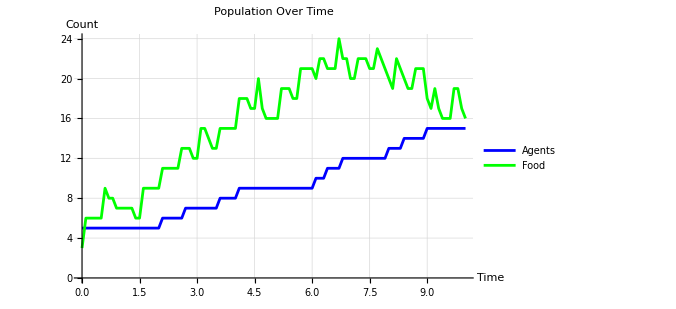

Part::partd: Part specification simulationGraphics[[101]]
     is longer than depth of object.

```mathematica
model = initializeModel[parameters];
Simulation = genSimulationStates[parameters, model, 100];
simulationGraphics = renderSimulation[Simulation, parameters];

Manipulate[simulationGraphics[[j]], {j, 1, Length@simulationGraphics, 1, Appearance->Labeled}]

plotPopulationStats[Simulation]
```

```mathematica
|
```

## Experimentation

## Conclusion

## Future Direction

## Acknowledgements

## References